```mathematica
(* (C) Copyright Aaron Goldberg,2022.

 This code is licensed under the Apache License,Version 2.0.You may
 obtain a copy of this license in the LICENSE.txt file in the root directory
 of this source tree or at http://www.apache.org/licenses/LICENSE-2.0.#

 Any modifications or derivative works of this code must retain this
 copyright notice,and modified files need to carry a notice indicating
 that they have been altered from the originals.
*)
```

```mathematica
(*Now let's try using TMSV full state and using PNRDs up to some N, calculate classical FI, see how much info is there. The probability of finding k,l photons in the distribution is sum N≥ k,l  of : ((1-eta1^2)/eta1^2)^(N-k)((1-eta2^2)/eta2^2)^(N-l)(eta1 eta2 Tanh[r])^(2N)Binomial[N,k]Binomial[N,l]/Cosh[r]^2*)
maxState=20;
maxPNRD=10;(*say we can only measure up to 5 photons or something, this will give us a lower bound*)
PNRDprobs=Table[Sum[((1-eta1^2)/eta1^2)^(NN-k)((1-eta2^2)/eta2^2)^(NN-l)(eta1 eta2 Tanh[r])^(2NN)Binomial[NN,k]Binomial[NN,l]/Cosh[r]^2,{NN,Max[k,l],maxState}],{k,0,maxPNRD},{l,0,maxPNRD}];
```

```mathematica
FIPNRD11=Total[D[PNRDprobs,eta1]*D[PNRDprobs,eta1]/PNRDprobs,2];
FIPNRD12=Total[D[PNRDprobs,eta1]*D[PNRDprobs,eta2]/PNRDprobs,2];
FIPNRD21=Total[D[PNRDprobs,eta2]*D[PNRDprobs,eta1]/PNRDprobs,2];
FIPNRD22=Total[D[PNRDprobs,eta2]*D[PNRDprobs,eta2]/PNRDprobs,2];
```

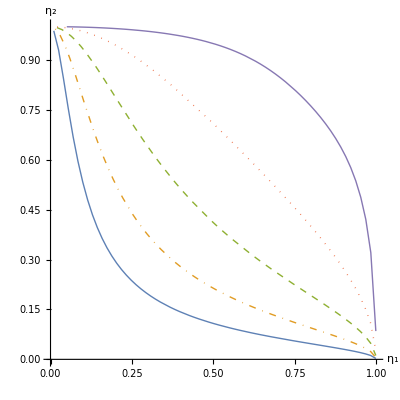

```mathematica
Block[{r=1/16},
p00625=Plot[eta2/.FindRoot[1/Tr[Inverse[{{FIPNRD11,FIPNRD12},{FIPNRD21,FIPNRD22}}]]-2Sinh[r]^2,{eta2,0.001,0.9999}],{eta1,0.01,0.999},MaxRecursion->5,PlotPoints->3,PlotRange-> {{0,1},{0,1}},PlotStyle->{ColorData[97,"ColorList"][[1]],Thick},AxesLabel-> {"η_1","η_2"},LabelStyle-> {Bold,Black,12},AspectRatio-> 1/GoldenRatio];
]
Block[{r=1/8},
p0125=Plot[eta2/.FindRoot[1/Tr[Inverse[{{FIPNRD11,FIPNRD12},{FIPNRD21,FIPNRD22}}]]-2Sinh[r]^2,{eta2,0.001,0.9995}],{eta1,0.015,0.999},MaxRecursion->5,PlotPoints->3,PlotRange-> {{0,1},{0,1}},PlotStyle->{ColorData[97,"ColorList"][[2]],DotDashed,Thick},AxesLabel-> {"η_1","η_2"},LabelStyle-> {Bold,Black,12},AspectRatio-> 1/GoldenRatio];
]
Block[{r=1/4},
p025=Plot[eta2/.FindRoot[1/Tr[Inverse[{{FIPNRD11,FIPNRD12},{FIPNRD21,FIPNRD22}}]]-2Sinh[r]^2,{eta2,0.001,0.999}],{eta1,0.02,0.999},MaxRecursion->5,PlotPoints->3,PlotRange-> {{0,1},{0,1}},PlotStyle->{ColorData[97,"ColorList"][[3]],Dashed,Thick},AxesLabel-> {"η_1","η_2"},LabelStyle-> {Bold,Black,12},AspectRatio-> 1/GoldenRatio];
]
Block[{r=1/2},
p05=Plot[eta2/.FindRoot[1/Tr[Inverse[{{FIPNRD11,FIPNRD12},{FIPNRD21,FIPNRD22}}]]-2Sinh[r]^2,{eta2,0.001,0.9999}],{eta1,0.02,0.999},MaxRecursion->5,PlotPoints->3,PlotRange-> {{0,1},{0,1}},PlotStyle->{ColorData[97,"ColorList"][[4]],Dotted,Thick},AxesLabel-> {"η_1","η_2"},LabelStyle-> {Bold,Black,12},AspectRatio-> 1/GoldenRatio];
]
Block[{r=1},
p1=Plot[eta2/.FindRoot[1/Tr[Inverse[{{FIPNRD11,FIPNRD12},{FIPNRD21,FIPNRD22}}]]-2Sinh[r]^2,{eta2,0.001,0.9999}],{eta1,0.05,0.999},MaxRecursion->5,PlotPoints->3,PlotRange-> {{0,1},{0,1}},PlotStyle->{ColorData[97,"ColorList"][[5]],Thin},AxesLabel-> {"η_1","η_2"},LabelStyle-> {Bold,Black,12},AspectRatio-> 1/GoldenRatio];
]
(*Block[{r=2},
p2=Plot[eta2/.FindRoot[1/Tr[Inverse[{{FIPNRD11,FIPNRD12},{FIPNRD21,FIPNRD22}}]]-2Sinh[r]^2,{eta2,0.001,0.9999}],{eta1,0.084,0.999},MaxRecursion->5,PlotPoints->3,PlotRange-> {{0,1},{0,1}},PlotStyle->{ColorData[97,"ColorList"][[6]],DotDashed,Thin},AxesLabel-> {"η_1","η_2"},LabelStyle-> {Bold,Black,12},AspectRatio-> 1/GoldenRatio];
]*)
Show[p00625,p0125,p025,p05,p1,AspectRatio-> 1]
```

```mathematica
Rasterize[Legended[Show[p00625,p0125,p025,p05,p1,AspectRatio-> 1,Epilog->{PointSize[Large],Point[{{0.392,0.382},{0.307,0.304},{0.368,0.372},{0.287,0.286}}]}],LineLegend[{Directive[ColorData[97,"ColorList"][[1]],Thick],{ColorData[97,"ColorList"][[2]],DotDashed,Thick},{ColorData[97,"ColorList"][[3]],Dashed,Thick},{ColorData[97,"ColorList"][[4]],Dotted,Thick},{ColorData[97,"ColorList"][[5]],Thin}
},{"r=1/16","r=1/8","r=1/4","r=1/2","r=1"}]]]
```

```mathematica
oneOverEtaTotalUncertaintyFull=1/(((-1+eta1^2) (-1+eta2^2-Csch[r]^2))/(4 eta2^2)+((-1+eta2^2) (-1+eta1^2-Csch[r]^2))/(4 eta1^2))//FullSimplify;
oneOverEtaTotalUncertaintyNoNuisance=1/(((-1+eta1^2) (eta1^2 (-1+eta2^2)+(-1-(-1+eta1^2) eta2^2) Csch[r]^2))/(4-4 eta2^2+eta1^2 (-4+8 eta2^2))+((-1+eta2^2) ((-1+eta1^2) eta2^2+(-1-eta1^2 (-1+eta2^2)) Csch[r]^2))/(4-4 eta2^2+eta1^2 (-4+8 eta2^2)))//FullSimplify;
```

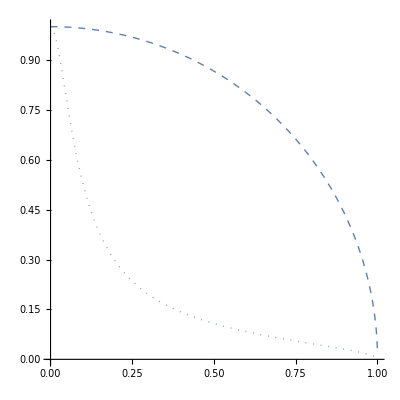

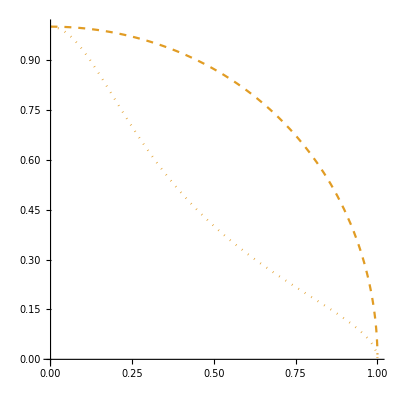

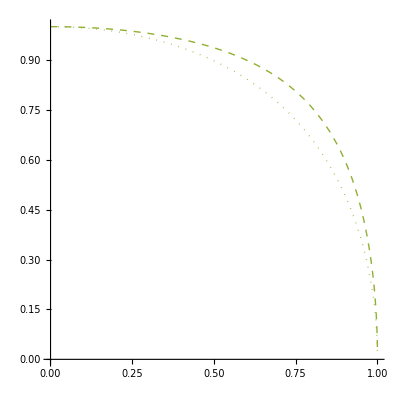

```mathematica
p00625QFI=Plot[{eta2/.NSolve[{(oneOverEtaTotalUncertaintyFull/.r-> 1/16/.eta1-> myeta1)==2Sinh[r]^2/.r-> 1/16,0≤ eta2≤ 1},eta2][[1]],eta2/.NSolve[{(oneOverEtaTotalUncertaintyNoNuisance/.r-> 1/16/.eta1-> myeta1)==2Sinh[r]^2/.r-> 1/16,0≤ eta2≤ 1},eta2][[1]]},{myeta1,0.001,0.9999},AspectRatio->1,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick,Dashed},{ColorData[97,"ColorList"][[1]],Thick,Dotted}}]
p025QFI=Plot[{eta2/.NSolve[{(oneOverEtaTotalUncertaintyFull/.r-> 1/4/.eta1-> myeta1)==2Sinh[r]^2/.r-> 1/4,0≤ eta2≤ 1},eta2][[1]],eta2/.NSolve[{(oneOverEtaTotalUncertaintyNoNuisance/.r-> 1/4/.eta1-> myeta1)==2Sinh[r]^2/.r-> 1/4,0≤ eta2≤ 1},eta2][[1]]},{myeta1,0.001,0.9999},AspectRatio->1,PlotStyle->{{ColorData[97,"ColorList"][[2]],Dashed},{ColorData[97,"ColorList"][[2]],Dotted}}]
p1QFI=Plot[{eta2/.NSolve[{(oneOverEtaTotalUncertaintyFull/.r-> 1/.eta1-> myeta1)==2Sinh[r]^2/.r-> 1,0≤ eta2≤ 1},eta2][[1]],eta2/.NSolve[{(oneOverEtaTotalUncertaintyNoNuisance/.r-> 1/.eta1-> myeta1)==2Sinh[r]^2/.r-> 1,0≤ eta2≤ 1},eta2][[1]]},{myeta1,0.001,0.9999},AspectRatio->1,PlotStyle->{{ColorData[97,"ColorList"][[3]],Thin,Dashed},{ColorData[97,"ColorList"][[3]],Thin,Dotted}}]
```

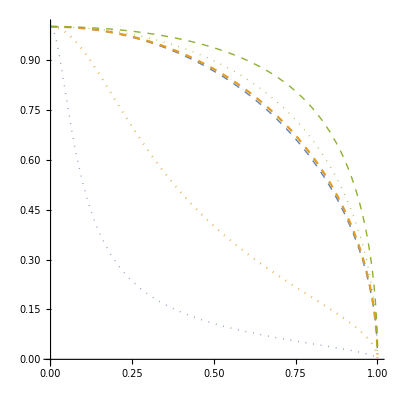

```mathematica
Show[p00625QFI,p025QFI,p1QFI]
```

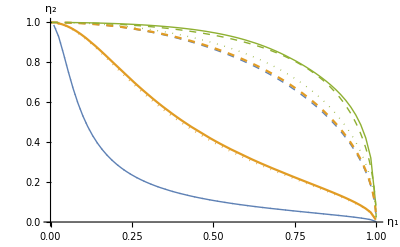

```mathematica
Block[{r=1/16},
p00625=Plot[eta2/.FindRoot[1/Tr[Inverse[{{FIPNRD11,FIPNRD12},{FIPNRD21,FIPNRD22}}]]-2Sinh[r]^2,{eta2,0.001,0.9999}],{eta1,0.01,0.999},MaxRecursion->5,PlotPoints->3,PlotRange-> {{0,1},{0,1}},PlotStyle->{ColorData[97,"ColorList"][[1]],Thick},AxesLabel-> {"η_1","η_2"},LabelStyle-> {Bold,Black,12},AspectRatio-> 1/GoldenRatio];
]
Block[{r=1/4},
p025=Plot[eta2/.FindRoot[1/Tr[Inverse[{{FIPNRD11,FIPNRD12},{FIPNRD21,FIPNRD22}}]]-2Sinh[r]^2,{eta2,0.001,0.999}],{eta1,0.02,0.999},MaxRecursion->5,PlotPoints->3,PlotRange-> {{0,1},{0,1}},PlotStyle->{ColorData[97,"ColorList"][[2]]},AxesLabel-> {"η_1","η_2"},LabelStyle-> {Bold,Black,12},AspectRatio-> 1/GoldenRatio];
]
Block[{r=1},
p1=Plot[eta2/.FindRoot[1/Tr[Inverse[{{FIPNRD11,FIPNRD12},{FIPNRD21,FIPNRD22}}]]-2Sinh[r]^2,{eta2,0.001,0.9999}],{eta1,0.05,0.999},MaxRecursion->5,PlotPoints->3,PlotRange-> {{0,1},{0,1}},PlotStyle->{ColorData[97,"ColorList"][[3]],Thin},AxesLabel-> {"η_1","η_2"},LabelStyle-> {Bold,Black,12},AspectRatio-> 1/GoldenRatio];
]
Show[p00625,p025,p1,p00625QFI,p025QFI,p1QFI]
```

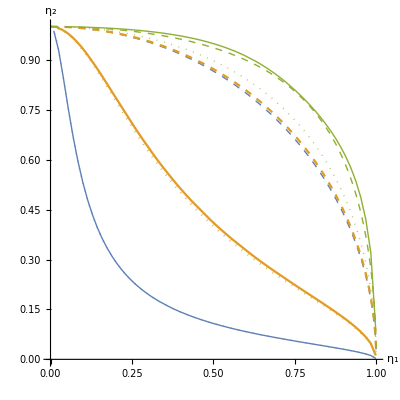

```mathematica
Show[p00625,p025,p1,p00625QFI,p025QFI,p1QFI,AspectRatio-> 1]
```

```mathematica
Rasterize[Legended[Show[p00625,p025,p1,p00625QFI,p025QFI,p1QFI,AspectRatio-> 1,Epilog->{PointSize[Large],Point[{{0.392,0.382},{0.307,0.304},{0.368,0.372},{0.287,0.286}}]}],LineLegend[{Directive[ColorData[97,"ColorList"][[1]],Thick],{ColorData[97,"ColorList"][[1]],Dashed,Thick},{ColorData[97,"ColorList"][[1]],Dotted,Thick},{ColorData[97,"ColorList"][[2]]},{ColorData[97,"ColorList"][[2]],Dashed},{ColorData[97,"ColorList"][[2]],Dotted},{ColorData[97,"ColorList"][[3]],Thin},{ColorData[97,"ColorList"][[3]],Dashed,Thin},{ColorData[97,"ColorList"][[3]],Dotted,Thin}
},{"r=1/16 PNRD","r=1/16 QFI varying r","r=1/16 QFI","r=1/4 PNRD","r=1/4 QFI varying r","r=1/4 QFI","r=1 PNRD","r=1 QFI varying r","r=1 QFI"}]]]
```